# Метод на допирателните (Нютон)

Дадено е уравнението:
(x^3 + px - (q + 50)sin3x  -2(p + q))/((x-1)(x+2))= 0, където p и q са съответно предпоследната и последната цифра от факултетния ни номер.
(x^3 + 6x + 43sin3x  -26)/((x-1)(x+2))= 0
=> Допустима област : 
x - 1 != 0  => x !=  1
x + 2 != 0 => x != -2
1. Да се намери общия брой на корените на уравнението.
2. Да се локализира най-големия реален корен в интервал [a, b].
3. Да се проверят условията за приложение на метода на допирателните (Нютон).
4. Да се определи началното приближение за итерационния процес по метода на допирателните (Нютон).
5. Да се изчисли корена по метода на допирателните с точност 10^-7. Представете таблица с изчисленията.
6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност.
7. Да се направи сравнение кой метод е по-ефективен за избрания интервал.

```mathematica
f[x_] := (x^3 + 6x + 43Sin[3x] - 26)/((x-1)(x+2))
```

```mathematica
f[x]
```

(-26+6 x+x^3+43 Sin[3 x])/((-1+x) (2+x))

## 1. Да се намери общия брой на корените на уравнението

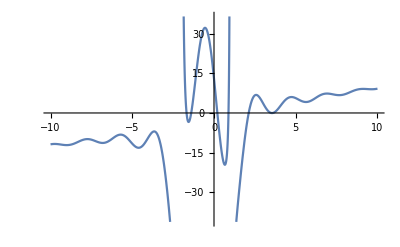

```mathematica
Plot[f[x], {x, -10, 10}]
```

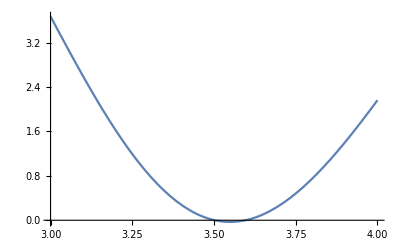

```mathematica
Plot[f[x], {x, 3, 4}]
```

Брой корени: 7

## 2. Да се локализира най-големия реален корен в интервала [a, b]

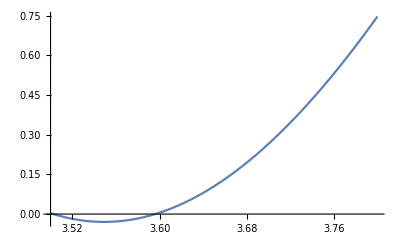

```mathematica
Plot[f[x], {x, 3.5, 3.8}]
```

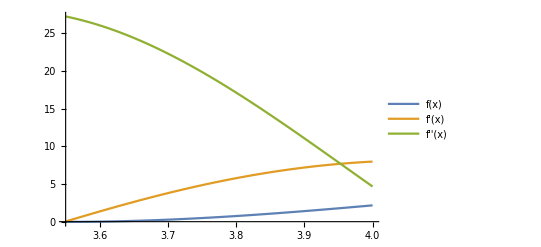

```mathematica
Plot[{f[x], f'[x], f''[x]}, {x,3.55, 4}, PlotLegends -> "Expressions" ]
```

```mathematica
f[3.55]
```

-0.0296069

```mathematica
f[4.]
```

2.16263

Извод:
1. f(3.55) = -0.029.. < 0
2. f(4) = 2.162.... > 0
Следователно в двата края на функцията има различни знаци и функцията е непрекъсната в избрания интервал [3.55;4]. Следва, че функцията има поне един корен в дадения интервал.

## 3. Проверка на условията за сходимост

### Проверка на първата производна

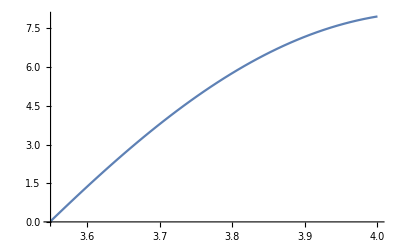

```mathematica
Plot[f'[x], {x, 3.55, 4}]
```

(1). Следва, че f'(x) има постоянен знак в дадения интервал.

### Проверка на втората производна

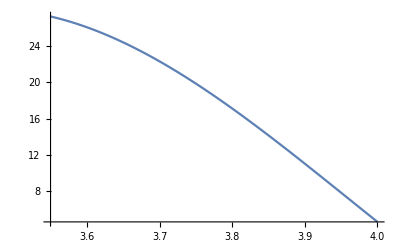

```mathematica
Plot[f''[x], {x, 3.55, 4}]
```

(1) . Следва, че f''(x) има постоянен знак в дадения интервал .

Извод: от (1) и (2) следва, че f'(x) и f''(x) са с постоянни знаци в разглеждания интервал [3.55; 4] => Методът на допирателните е сходящ.

## 4. Избор на начално приближение

f(x_0) * f’’ > 0
=> f(x_0) < 0
=> x_0 = 3.55

### Пресмятане на постоянните величини:

```mathematica
Plot[Abs[f''[x]], {x, 3.55, 4}]
```

-Graphics-

От геометрични съображения максимума се достига в левия край на интервала, а минимума - в десния.

```mathematica
М2 = Abs[f''[3.55]]
```

27.2093

```mathematica
Plot[Abs[f'[x]], {x, 3.55, 4}]
```

-Graphics-

От геометрични съображения максимума се достига в десния край на интервала, а минимума - в левия .

```mathematica
m1 = Abs[f'[4.]]
```

7.9663

```mathematica
p = М2/(2m1)
```

1.70777

## 5.Да се изчисли корена по метода на допирателните с точност 10^-7

```mathematica
f[x_]:=   (x^3 + 6x + 43Sin[3x] - 26)/((x-1)(x+2))
x0 = 3.55;
М2 = Abs[f''[3.55]];
m1 = Abs[f'[4.]];
p = М2/(2m1);
epszad = 0.0000001;
eps = 1;
Print["n = ",0,  " x_n = ", x0, " f(x) = ", f[x0], " f'(x) = ", f'[x0]];
For[n = 1, eps > epszad, n++,
x1 = x0 - f[x0]/f'[x0];
Print["n = ",n,  " x_n = ", x1, " f(x_n) = ", f[x1] " f'(x_n) = ", f'[x1], " ε_n = ", eps = p* (x1 - x0)^2];
x0 = x1
]
```

n = 0 x_n = 3.55 f(x) = -0.0296069 f'(x) = 0.0247471

n = 1 x_n = 4.74638 f(x_n) = 6.02116  f'(x_n) = -0.1078 ε_n = 2.44436

n = 2 x_n = 60.6016 f(x_n) = 59.7357  f'(x_n) = 1.02976 ε_n = 5327.91

n = 3 x_n = 2.59228 f(x_n) = 6.81679  f'(x_n) = -0.828207 ε_n = 5746.79

n = 4 x_n = 10.8231 f(x_n) = 10.6707  f'(x_n) = 1.42574 ε_n = 115.694

n = 5 x_n = 3.33868 f(x_n) = 0.582997  f'(x_n) = -5.7776 ε_n = 95.6624

n = 6 x_n = 3.43959 f(x_n) = 0.136306  f'(x_n) = -3.04257 ε_n = 0.0173887

n = 7 x_n = 3.48439 f(x_n) = 0.0280431  f'(x_n) = -1.79013 ε_n = 0.00342751

n = 8 x_n = 3.50005 f(x_n) = 0.00342653  f'(x_n) = -1.3529 ε_n = 0.000419096

n = 9 x_n = 3.50258 f(x_n) = 0.0000893427  f'(x_n) = -1.28235 ε_n = 0.000010955

n = 10 x_n = 3.50265 f(x_n) = 6.75728×10^-8  f'(x_n) = -1.28041 ε_n = 8.28958×10^-9

## 6. Да се провери колко итерации биха били необходими, ако се използва метода на разполовяването в същия интервал [a, b] за същата точност

```mathematica
Log2[(4 - 3.55)/0.0000001] - 1
```

21.1015

## 6. Да се направи сравнение кой метод е по-ефективен за избрания интервал

Извод: По метода на допирателните (Нютон) биха били необходими 10 итерации за достигане на исканата точност. А по метода на разполовяването са необходими 22 итерации. Следователно методът на допирателните е по-ефективен за избрания интервал [3.55, 4].